```mathematica
SetDirectory[NotebookDirectory[]]
Import["GraphPartition.m"]
<< GraphPartition`
$Context
```

C:\Users\Chuqian\Desktop\research\graphPartitioning

Global`

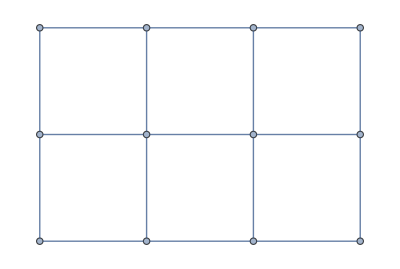

```mathematica
g = System`GridGraph[{3,4}]
```

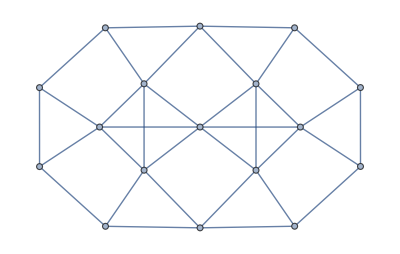

```mathematica
System`LineGraph[g]
```

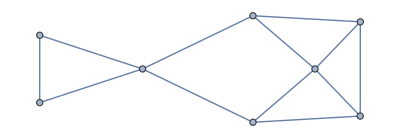
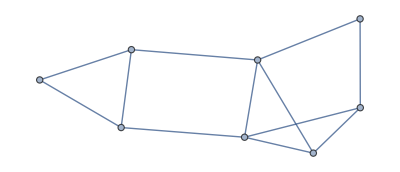
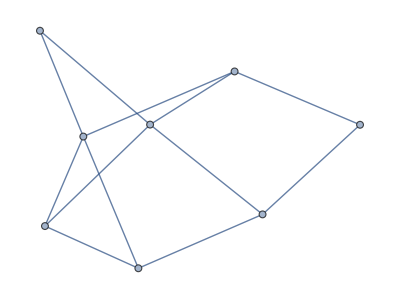

```mathematica
System`RandomGraph[DegreeGraphDistribution[{3,4,2,3,3,4,2,3}],3]
```

```mathematica
(*Neighbors[i_,j_, m_,n_,dist_] := Select[Complement[Flatten[Table[{i+di, i+dj},{di,-dist,dist},{dj,-dist,dist}],1],{{i,j}}],
1<=First[#]<=5 && 1≤Last[#]≤4 &]*)
```

{{1,11},{1,9},{2,3},{2,8},{3,8},{3,12},{4,11},{4,7},{5,11},{5,9},{6,10},{7,11},{7,9},{8,16},{8,7},{9,3},{9,15},{10,5},{10,13},{11,3},{11,2},{12,4},{13,6},{13,14},{14,5},{15,5},{16,14},{16,6}}

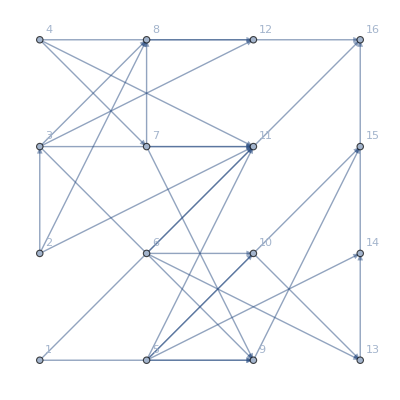

```mathematica
m=4;
n=4;
maxDist = 2;
maxDegree = 2;
vlist = Range[1,m*n];
vcoords= Flatten[Table[{i,j},{i,1,m},{j,1,n}],1];
elist = {};
Vertex1D[ij_,m_,n_] := (First[ij]-1)*n+Last[ij]
Neighbors[i_,j_, m_,n_,dist_] := Select[Flatten[Table[{i+di, j+dj},{di,-dist,dist},{dj,-dist,dist}],1],
1<=First[#]≤m && 1≤Last[#]≤n && #≠{i,j}&]
Do[With[{newE = {Vertex1D[{i,j},m,n],Vertex1D[adj,m,n]}},
AppendTo[elist,newE]],{i,1,m},{j,1,n},{adj, RandomChoice[Neighbors[i,j,m,n,maxDist],maxDegree]}]
elist =DeleteDuplicates[elist,#1==#2||#1==Reverse[#2]& ]
newG=System`Graph[vlist,elist,VertexCoordinates->vcoords,
System`VertexWeight->Table[1/Length[vlist], Length[vlist]],System`EdgeWeight-> Table[1,Length[elist]],
System`VertexLabels->Automatic,
System`EdgeStyle->Directive[Opacity[0.5], Thick], EdgeShapeFunction->"Arrow"];
newG = UndirectedGraph[newG]
(*Map[#->PropertyValue[{g,#}]]*)
```

```mathematica
m=3;n=3;
g= System`GridGraph[{m,n},System`EdgeStyle->Directive[Dashed,Thick]
(*, EdgeShapeFunction->"Arrow"*)];
VertexDistance[i_,j_,m_,n_] :=
 With[{x1=Mod[i-1,m], x2=Mod[j-1,m],y1=Quotient[i-1,m],y2=Quotient[j-1,m]},
((x1-x2)^2+(y1-y2)^2)^(1/2)]
newE = Flatten[Table[UndirectedEdge[i,j],{i,1,m*n-1},
{j, RandomChoice[
Select[Range[i+1,m*n],0<VertexDistance[i,#,m,n]≤4&]
,RandomInteger[{0,2}]]}],1];
g=System`EdgeAdd[g,newE]
```

-Graphics-

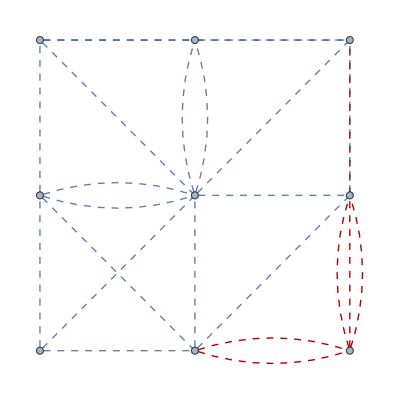

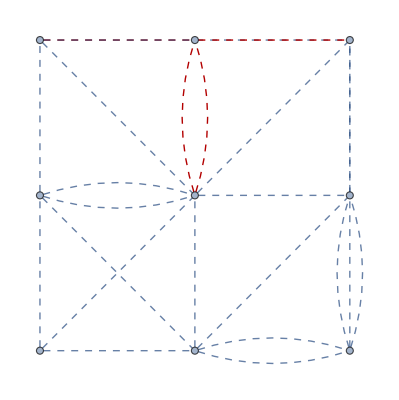

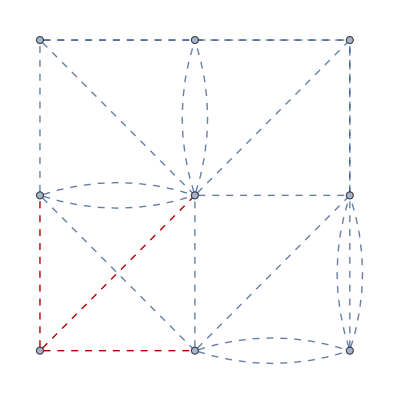

```mathematica
(*GG = System`GridGraph[{3,4}, VertexLabels->Automatic,VertexWeight->Table[1/12,12]]*)
(*ShowSpectralCut[newG]*)
ShowSpectralCut[g]
ShowIsoperimetricCut[g]
ShowMultipleFiedlerCut[g]
```

```mathematica
EdgeList[newG]
```

{1<->10,2<->7,2<->1,3<->6,3<->7,4<->10,4<->12,5<->2,5<->7,6<->4,6<->8,7<->15,7<->14,8<->12,8<->16,9<->5,9<->3,10<->14,11<->10,11<->1,12<->16,13<->6,13<->9,14<->12,14<->15,15<->9,15<->5,16<->15,16<->7}

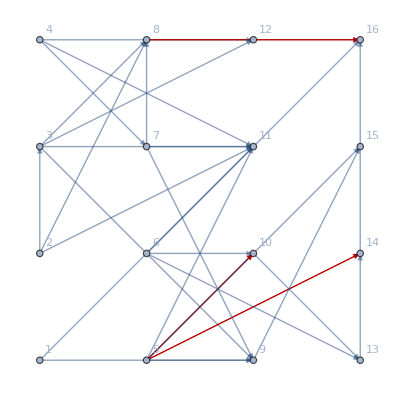

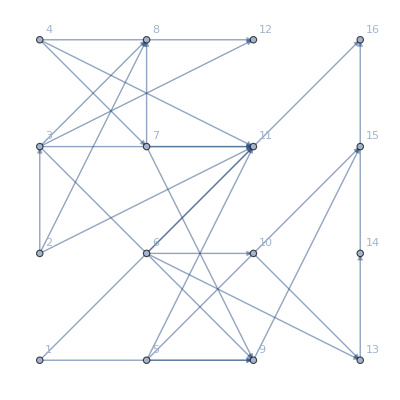

{1<->11,1<->9,2<->3,2<->8,3<->8,3<->12,4<->11,4<->7,5<->11,5<->9,6<->10,7<->11,7<->9,8<->16,8<->7,9<->3,9<->15,10<->5,10<->13,11<->3,11<->2,12<->4,13<->6,13<->14,14<->5,15<->5,16<->14,16<->6}

{0.985603,1.12303,1.07637,1.12388,0.82832,1.1703,1.05698,1.13283,0.811316,1.08598,1.05058,1.15478,1.15,1.08442,0,1.16562}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,16}

{0.240731,768/55}

{8<->16,10<->5,14<->5}

```mathematica
ShowSpectralCut[newG]
SpectralCut[newG]
EdgeList[newG]
v=IsoperimetricVector[newG]
cutoff=0.136569;
Select[Table[i,{i,1,Length[v]}], v[[#]]≥cutoff&]
CriterionCut[newG, FiedlerVector[newG],IncludeCut->True]
VectorCut[newG, FiedlerVector[newG], cutoff]
```

```mathematica
SimpleGraphQ[%1510]
```

True

```mathematica
FindClique[%1510]
```

{{1,10,11}}

```mathematica
ConnectedComponents[%1510]
```

{{3,6,7,9,4,8,13,5,15,14,16,12},{1,10,2,11}}

```mathematica
v[[1]]
v[[2]]
```

0.458644

0.136569

```mathematica
Plot performances on GridGraphs
```

```mathematica
SquareGrid[n_] := System`GridGraph[{n,n}, 
VertexLabels->If[n<10,Automatic,None],VertexWeight->Table[1/n/n,n*n], EdgeWeight->Automatic];
graphs = Map[SquareGrid[#]&, Range[5,10,2]];

SpectralMetrics = Map[EvaluatePartitionAlg[SpectralAlg, #]&, graphs];
SpectralTimes = Transpose[SpectralMetrics][[1]]
SpectralObjs = Transpose[SpectralMetrics][[2]]
IsoperimetricMetrics = Map[EvaluatePartitionAlg[IsoperimetricAlg, #]&, graphs];
IsoperimetricTimes = Transpose[IsoperimetricMetrics][[1]]
IsoperimetricObjs = Transpose[IsoperimetricMetrics][[2]]
MultipleFiedlerMetrics = Map[EvaluatePartitionAlg[MultipleFiedlerAlg, #]&, graphs];
MultipleFiedlerTimes = Transpose[MultipleFiedlerMetrics][[1]]
MultipleFiedlerObjs = Transpose[MultipleFiedlerMetrics][[2]]
```

{0.,0.03125,0.078125}

{1875/68,2401/60,6561/164}

{0.015625,0.03125,0.09375}

{625/26,4802/93,59049/610}

{0.09375,0.6875,3.53125}

{125/6,343/12,729/20}

{Spectral,Isoperimetric,MultipleFiedler}

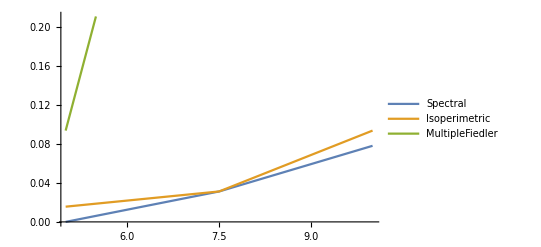

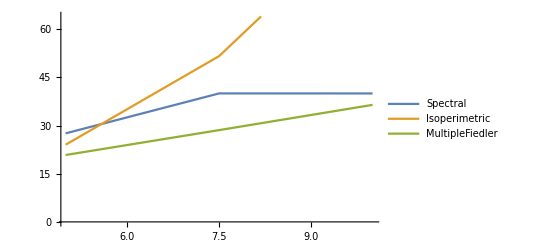

```mathematica
legends = {"Spectral","Isoperimetric","MultipleFiedler"}
ListLinePlot[{SpectralTimes, IsoperimetricTimes, MultipleFiedlerTimes},PlotLegends->legends, DataRange->{5,10}]
ListLinePlot[{SpectralObjs, IsoperimetricObjs, MultipleFiedlerObjs}, PlotLegends->legends, DataRange->{5,10}]
```